```mathematica
SetDirectory["/Users/sinbi/desktop/STUDY/Data_get/bb"];
Needs["ErrorBarPlots`"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ErrorBarLogPlots.m"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ProtonFluxELDRAnn.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## AMS02-Experiment Error Bar Import

57

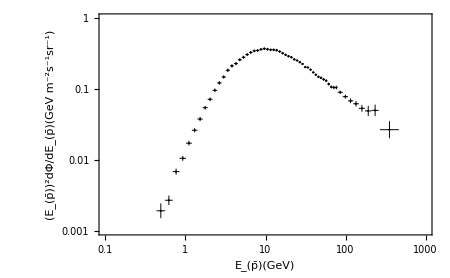

```mathematica
IErrorb= Import["/Users/sinbi/desktop/study/Data_get/Error_data_AMS02_Full.dat","Table",HeaderLines-> 1];
Length[IErrorb]
IErrorb1=Table[{IErrorb[[i,1]],IErrorb[[i,2]],(IErrorb[[i,4]]-IErrorb[[i,3]])/2,(IErrorb[[i,6]]-IErrorb[[i,5]])/2},{i,1,Length[IErrorb]}];
IErrorb2=IErrorb1/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
ErroPlotb=ErrorListLogLogPlot[IErrorb2,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-3,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Get Background(BG)

350

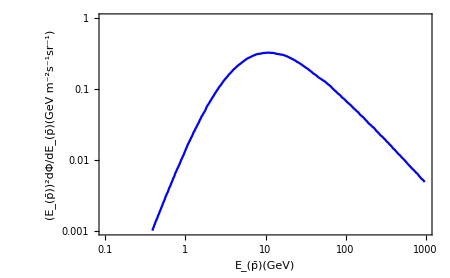

```mathematica
BGb=Import["/Users/sinbi/desktop/study/Data_get/DRC_AMS.txt","Table","HearderLines"->1];
Length[BGb]
ifBGb=Interpolation[BGb];
BGPlotb=ListLogLogPlot[ifBGb,Joined->True,Axes->False,Frame->True,PlotRange->{{10^-1,10^3},{10^-3,1}},ImageSize->450,PlotStyle->{Blue},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

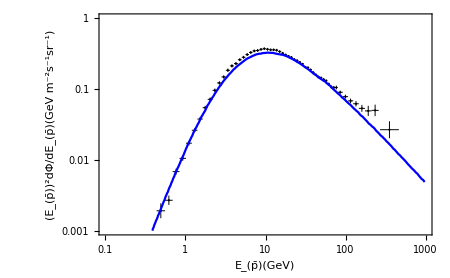

```mathematica
Show[ErroPlotb,BGPlotb,FrameTicksStyle->Directive[Black, Bold, 13], FrameLabel->{Style["E_(p̄)(GeV)",15,Black,Bold, FontFamily->Times],Style["(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)",15,Black,Bold, FontFamily->Times]}]
```

## Dark Matter(DM)

```mathematica
primaryb="b";
halob="NFW";
propagationb="MED";
mDMb=73.54;
σvb=10^-26;
Eγ=10^lEγ;
```

```mathematica
ifPob=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primaryb, halob, propagationb][mDMb, σvb,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

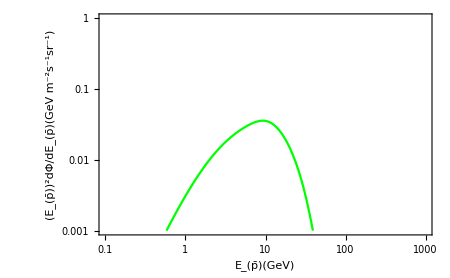

977.237

```mathematica
PlotMEDb=ListLogLogPlot[ifPob,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicksStyle->Directive[Black, Bold, 13], FrameLabel->{Style["E_(p̄)(GeV)",15,Black,Bold, FontFamily->Times],Style["(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)",15,Black,Bold, FontFamily->Times]}]
10^2.99
```

## SUM=BG+DM

InterpolatingFunction[…]

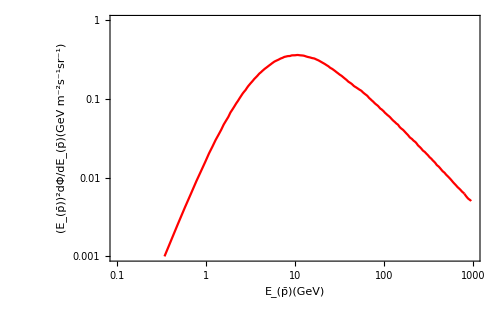

```mathematica
Sumdatab=Interpolation[Table[{x,ifBGb[x]+ifPob[x]},{x,0.18,10^2.98,0.1}]]
SumPlotb=ListLogLogPlot[Sumdatab,Joined->True,PlotRange->{{10^-1,10^3},{10^-3,1}},PlotStyle->Red,Frame->True,Axes->False,ImageSize->500 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

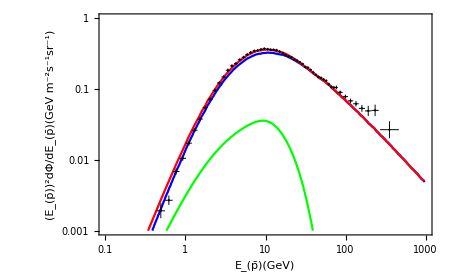

```mathematica
Show[BGPlotb,PlotMEDb,SumPlotb,ErroPlotb,FrameTicksStyle->Directive[Black, Bold, 13], FrameLabel->{Style["E_(p̄)(GeV)",15,Black,Bold, FontFamily->Times],Style["(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)",15,Black,Bold, FontFamily->Times]}]
```

## χ^2- Fitting

```mathematica
SumYb=Table[Sumdatab[IErrorb1[[i,1]]],{i,Length[IErrorb]}];
IErrorYb=Flatten[Table[{IErrorb1[[i,2]]},{i,1,Length[IErrorb]}],1];
IErrorSizeb=Flatten[Table[{IErrorb1[[i,4]]},{i,1,Length[IErrorb]}],1];chiSUMb=((SumYb-IErrorYb)/IErrorSizeb)^2;
Sum1=Sum[chiSUMb[[i]],{i,1,Length[IErrorb]}]
Re[Sum1]
```

137.564+0. ⅈ

137.564

## Mass-σv graph

```mathematica
ClearAll[σv02]
```

```mathematica
mDM02=10^lmDM02;
```

```mathematica
σv02=10^lσv02;
```

```mathematica
ifPob2=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primaryb, halob, propagationb][mDM02, σv02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

```mathematica
Sumdatab2=Interpolation[Table[{x,ifBGb[x]+ifPob2[x]},{x,0.18,10^2.98,0.1}]];
SumYb2=Table[Sumdatab2[IErrorb1[[i,1]]],{i,Length[IErrorb]}];
chiSUMb2=((SumYb2-IErrorYb)/IErrorSizeb)^2;
FinalSumb=Sum[chiSUMb2[[i]],{i,1,Length[IErrorb]}];
```

```mathematica
contb=Flatten[Table[Re[{mDM02,lσv02,σv02,FinalSumb}],{lmDM02,0.7,2.4,0.02},{lσv02,-29,-24.5,0.02}], 1];
Export["bb_NFW_MED_DRC.dat",contb,"Table"];
```

```mathematica
contableb=Import["/Users/sinbi/desktop/study/Data_get/bb/bb_NFW_MED_DRC.dat","Table",HeaderLines->1]
```

{{5.01187,-28.98,1.04713×10^-29,191.259},{5.01187,-28.96,1.09648×10^-29,191.259},{5.01187,-28.94,1.14815×10^-29,191.26},{5.01187,-28.92,1.20226×10^-29,191.26},{5.01187,-28.9,1.25893×10^-29,191.26},19426,{251.189,-24.56,2.75423×10^-25,13347.7},{251.189,-24.54,2.88403×10^-25,14713.6},{251.189,-24.52,3.01995×10^-25,16215.8},{251.189,-24.5,3.16228×10^-25,17867.7}}
 |  |  |  |

```mathematica
contbLog=Table[{contableb[[i,1]],contableb[[i,2]], contableb[[i, 4]]},{i, Length[contableb]}];
```

```mathematica
Export["bb_table_NFW_MED_DRC.dat",contbLog,"Table"]
```

bb_table_NFW_MED_DRC.dat

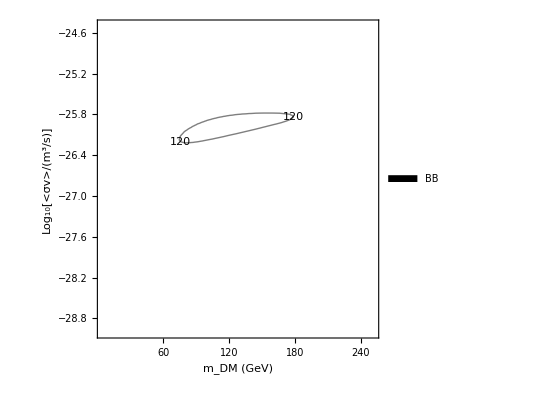

```mathematica
ListContourPlot[contbLog,Contours-> {60, 65,70,80,120},
FrameLabel->{"m_DM (GeV)","Log_10[<σv>/(m^3/s)]"}, ContourLabels->All,ContourShading->None,PlotLegends->Placed[SwatchLegend[{"BB"},LegendMarkerSize->20],Right]]
```